```mathematica
f[x_]:=x^2-5
```

```mathematica
f[5]
```

20

```mathematica
g[x_]:=(Cos[x]-Sin[x])/x
```

```mathematica
g[5]
```

```mathematica
1/5 (Cos[5]-Sin[5])
N[g[3]]
```

1/5 (Cos[5]-Sin[5])

-0.377038

```mathematica
Plot[-x^2-4, {x, -3, 3}]
```

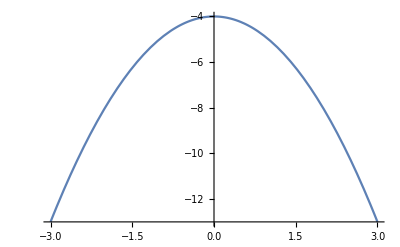
```mathematica
-Graphics-
Plot[g[x], {x, -2π, 2π}]
```

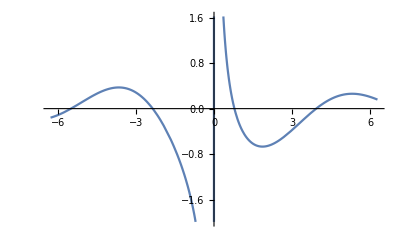
```mathematica
-Graphics-
Plot[g[x], {x, -2π, 2π}, PlotStyle->RGBColor[0.25,0.35,0.5], PlotRange->{-10, 10}]
```

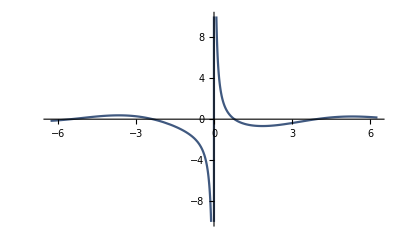
```mathematica
-Graphics-
Plot[x^2 + 5, {x, -3, 3}, PlotRange->{-10, 10}, PlotStyle->Green, AxesOrigin->{0,0}]
```

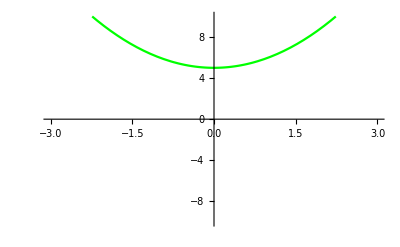
```mathematica
-Graphics-
Plot[{Log[x],Tan[x], x^3-7x+20}, {x, 1.4, 1.6}, PlotLegends->"Expressions", PlotRange->{12.8,13}]
```

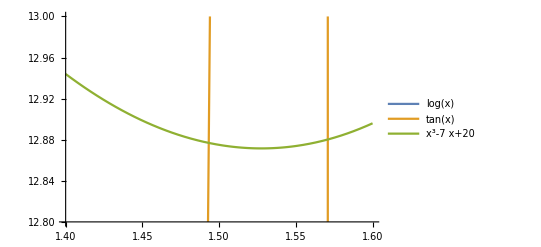

```mathematica
Plot[{Log[x],Tan[x], x^3-7x+20}, {x, 1.4, 1.6}, PlotLegends->"Expressions", PlotRange->{12.8,13}]
```

```mathematica
Plot[{Log[x],Tan[x], x^3-7x+20}, {x, 1.4, 1.6}, PlotLegends->"Expressions", PlotRange->{12.8,13}]
```

-Graphics-

```mathematica
f[x_]:=(x^3-5 x^2+3x+1)/(2 x^2+x-1)
```

```mathematica
g[x_]:= x
```

```mathematica
h[x_]:= Sin[x]^4+Cos[x]^4
```

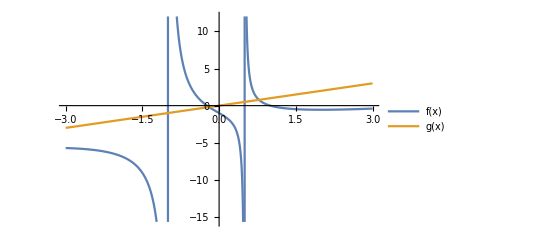

```mathematica
Plot[{f[x], g[x]}, {x, -3, 3}, PlotLegends->"Expressions"]
```

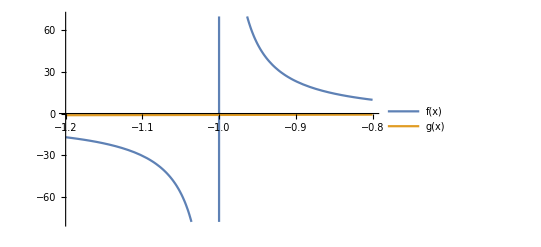

Plot::nonopt: Options expected (instead of Plot) beyond position 2 in Plot[{f[x],g[x]},{x,-1.2,-0.8},PlotLegends→Expressions,Plot]. An option must be a rule or a list of rules.

Plot[{f[x],g[x]},{x,-1.2,-0.8},PlotLegends→Expressions,Plot]

```mathematica
Plot[{f[x], g[x]}, {x, -1.2, -0.8}, PlotLegends->"Expressions"]
```

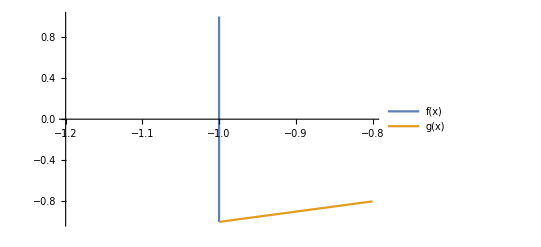

```mathematica
Plot[{f[x], g[x]}, {x, -1.2, -0.8}, PlotLegends->"Expressions", PlotRange->{-1, 1}]
```

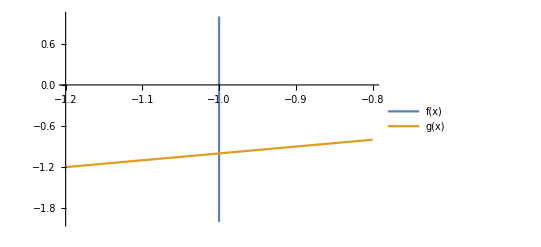

```mathematica
Plot[{f[x], g[x]}, {x, -1.2, -0.8}, PlotLegends->"Expressions", PlotRange->{-1.5, 1}]
```

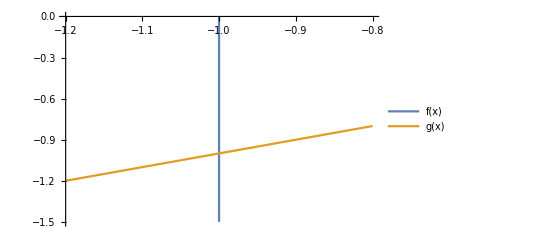

```mathematica
Plot[{f[x], g[x]}, {x, -1.2, -0.8}, PlotLegends->"Expressions", PlotRange->{-1.5, 0}]
```

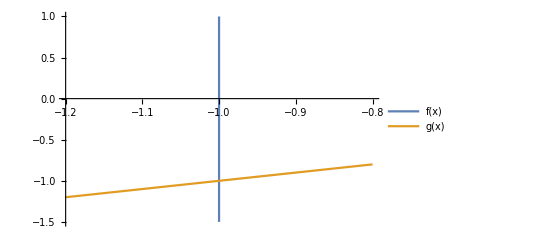

```mathematica
Plot[{f[x], g[x]}, {x, -1.2, -0.8}, PlotLegends->"Expressions", PlotRange->{-1.5, 1}]
```

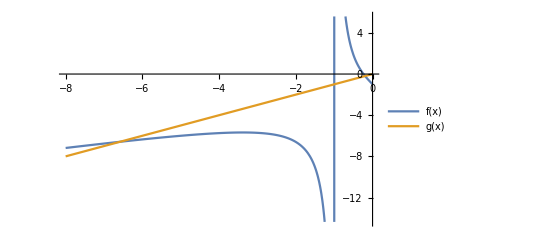

```mathematica
Plot[{f[x], g[x]}, {x, -8, 0}, PlotLegends->"Expressions", AxesOrigin->{0,0}]
```

```mathematica
j[x_]:=e^-x
```

```mathematica
k[x_]:=Log[x^2]
```

```mathematica
Plot[{j[x_], k[x_]}, {x, -5, 5}, PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Limit[ArcTan[x], x->-∞]
```

-π/2

```mathematica
Limit[ArcTan[x], x->+∞]
```

π/2

```mathematica
Plot[{ArcTan[x], π/2, -π/2}, (x, -10, 10), PlotStyle->{Automatic, Dashed, Dashed}, PlotLegends->"Expressions"]
```

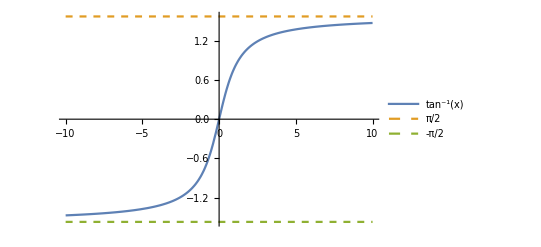

```mathematica
Plot[{ArcTan[x], π/2, -π/2}, {x, -10, 10}, PlotStyle->{Automatic, Dashed, Dashed}, PlotLegends->"Expressions"]
```

```mathematica
Plot[f[x_], {x, 10, 10}]
```

Plot::plld: Endpoints for x in {x,10,10} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Plot[f[x_],{x,10,10}]

```mathematica
f[x_]:=(x^3-5 x^2+3x+1)/(2 x^2+x-1)
```

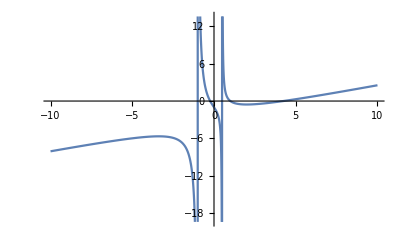

```mathematica
Plot[f[x], {x, -10, 10}]
```

```mathematica
Limit[f[x], x->-1, Direction->1]
```

-∞

```mathematica
Limit[f[x], x->-1, Direction->-1]
```

∞

```mathematica
Limit[f[x], x->1, Direction->1]
```

0

```mathematica
Limit[f[x], x-> 0,5, Direction->1]
```

Limit::nonopt: Options expected (instead of 5) beyond position 2 in Limit[(1+3 x-5 x^2+x^3)/(-1+x+2 x^2),x→0,5,Direction→1]. An option must be a rule or a list of rules.

Limit[(1+3 x-5 x^2+x^3)/(-1+x+2 x^2),x→0,5,Direction→1]

```mathematica
Limit[f[x], x->∞]
```

∞

```mathematica
Limit[f[x], x->-∞]
```

-∞

```mathematica
q[x_]=log((x^2-1)/(2x-3))
```

(log (-1+x^2))/(-3+2 x)

```mathematica
q[x_]:=log((x^2-1)/(2x-3))
```

```mathematica
Polt[q[x], {x, -10, 10}]
```

Polt[(log (-1+x^2))/(-3+2 x),{x,-10,10}]

```mathematica
Plot[log((x^2-1)/(2x-3)), {x, 0, 100}]
```

-Graphics-

```mathematica
f[x]-f[-x]
```

-(1-3 x-5 x^2-x^3)/(-1-x+2 x^2)+(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
g[x]+g[-x]
```

```mathematica
g[-x]+g[x]
g[x_]:= x
```

g[-x]+g[x]

```mathematica
g[x]+g[-x]
```

0

```mathematica
h[x]+h[-x]
```

h[-x]+h[x]

```mathematica
h[x_]:= Sin[x]^4+Cos[x]^4
```

```mathematica
h[x]+h[-x]
```

2 Cos[x]^4+2 Sin[x]^4

```mathematica
h[x]-h[-x]
```

0

```mathematica
k[x_]:=Log[(x^2-1)/(2x-3)]
```

```mathematica
k[x]
```

Log[(-1+x^2)/(-3+2 x)]

```mathematica
FunctionDomain[k[x],x]
```

-1<x<1||x>3/2

```mathematica
Limit[k[x], x->∞]
```

∞

```mathematica
Limit[k[x], x-> 1]
```

-∞

```mathematica
Limit[k[x], x->(3/2)]
```

∞

```mathematica
Limit[k[x], x-> -1]
```

-∞

```mathematica
Limit[k[x], x->-∞]
```

∞

```mathematica
F[x_]:=(x^3-3x^2+x+1)/(x^2+3x-10)
```

```mathematica
G[x_]:=x
```

```mathematica
H[x_] := sin(x)*cos^2(x)
```

```mathematica
H[x]
```

cos^2 sin x^2

```mathematica
H[x_]:=sin(x)*cos(x)^2
```

```mathematica
H[x]
```

cos sin x^3

```mathematica
H[x_]:=Sin[x]*Cos[x]^2
```

```mathematica
H[x]
```

Cos[x]^2 Sin[x]

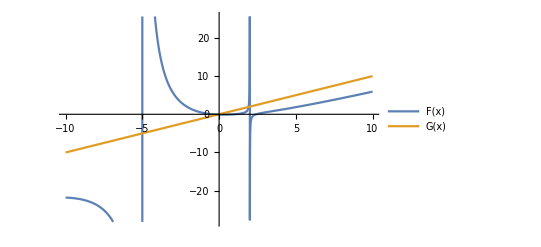

```mathematica
Plot[{F[x],G[x]},{x, -10, 10},PlotLegends->"Expressions"]
```

```mathematica
Plot[{e^-x, log[x]}, {x,-10,10}, PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
J[x_]:=e^-x
```

```mathematica
K[x_]:=Log[x]
```

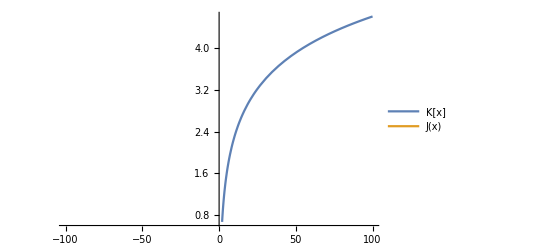

```mathematica
Plot[{K[x], J[x]},{x, -100, 100}, PlotLegends->"Expressions"]
```

```mathematica
J[x]
```

e^-x

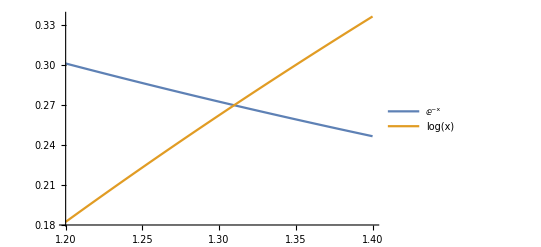

```mathematica
Plot[{E^-x,Log[x]},{x, 1.2, 1.4}, PlotLegends->"Expressions"]
```

```mathematica
Limit[F[x],x->∞]
```

∞

```mathematica
Limit[F[x], x->-∞]
```

-∞

```mathematica
FunctionDomain[F[x], x]
```

x<-5||-5<x<2||x>2

```mathematica
Limit[F[x], x->-5, Direction->1]
```

-∞

```mathematica
Limit[F[x], x->-5, Direction->-1]
```

∞

```mathematica
Limit[F[x], x-> 2, Direction->1]
```

∞

```mathematica
Limit[F[x], x->2, Direction->-1]
```

-∞

```mathematica
Limit[F[x]/x, x->Infinity]
```

1

```mathematica
Limit[F[x]-x*1, x->Infinity]
```

-6

```mathematica
Limit[F[x]/x, x->-Infinity]
```

1

```mathematica
Limit[F[x]-x, x->-Infinity]
```

-6

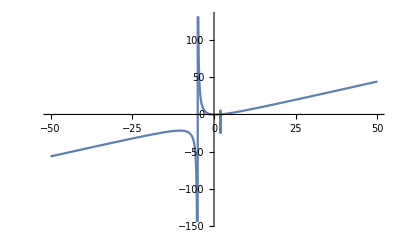

```mathematica
Plot[F[x], {x, -50, 50}]
```

```mathematica
Q[x_]:=(1-5x^2)/(4-x^2)
```

```mathematica
FunctionDomain[Q[x], x]
```

x<-2||-2<x<2||x>2

```mathematica
Limit[Q[x], x-> -2, Direction->1]
```

∞

```mathematica
Limit[Q[x], x-> -2, Direction->-1]
```

-∞

```mathematica
Limit[Q[x], x-> 2, Direction->1]
```

-∞

```mathematica
Limit[Q[x], x-> 2, Direction->-1]
```

∞

```mathematica
Limit[Q[x]/x, x->-Infinity]
```

0

```mathematica
Limit[Q[x], x-> Infinity]
```

5

```mathematica
Limit[Q[x], x-> -Infinity]
```

5

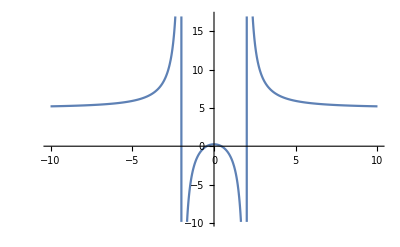

```mathematica
Plot[Q[x], {x, -10, 10}]
```

```mathematica
Simplify[F[x]+F[-x]]
```

-(4 (5-14 x^2+3 x^4))/(100-29 x^2+x^4)

```mathematica
Simplify[F[x]-F[-x]]
```

(2 x (-13+x^4))/(100-29 x^2+x^4)

```mathematica
Simplify[G[x]+G[-x]]
```

0

```mathematica
Simplify[H[x]+H[-x]]
```

0